## Define dist

```mathematica
Solve[c/(b^a+1)==1,c]
```

{{c→1+b^a}}

```mathematica
testDist[x_,a_,b_]:=(1+b^a)/((x+b)^a+1)
```

```mathematica
testDistRB[RB_,a_,b_]:=(1+b^a)/(b^a RB^a+1) (*RB=(x+b)/b=x/b+1*)
```

```mathematica
testDistRBExp[RB_,a_,b_]:=(1+b^a)/(b^a Exp[a (RB-1)]+1) (*RB=(x+b)/b=x/b+1*)
```

## Define families of funcs

### The x version

```mathematica
funcsShiftA=MapThread[testDist][{{x,x,x,x},{1,2,3,4},{1,1,1,1}}]
```

{2/(2+x),2/(1+(1+x)^2),2/(1+(1+x)^3),2/(1+(1+x)^4)}

```mathematica
funcsShiftB1=MapThread[testDist][{{x,x,x,x},{1,1,1,1},{1,2,3,4}}]
```

{2/(2+x),3/(3+x),4/(4+x),5/(5+x)}

```mathematica
funcsShiftBA[a_]:=MapThread[testDist][{{x,x,x,x,x},{a,a,a,a,a},{15,9,5,3,1}}]
```

```mathematica
funcsShiftB1=funcsShiftBA[1]
funcsShiftB2=funcsShiftBA[2]
funcsShiftB3=funcsShiftBA[3]
funcsShiftB4=funcsShiftBA[4]
```

{16/(16+x),10/(10+x),6/(6+x),4/(4+x),2/(2+x)}

{226/(1+(15+x)^2),82/(1+(9+x)^2),26/(1+(5+x)^2),10/(1+(3+x)^2),2/(1+(1+x)^2)}

{3376/(1+(15+x)^3),730/(1+(9+x)^3),126/(1+(5+x)^3),28/(1+(3+x)^3),2/(1+(1+x)^3)}

{50626/(1+(15+x)^4),6562/(1+(9+x)^4),626/(1+(5+x)^4),82/(1+(3+x)^4),2/(1+(1+x)^4)}

### The RB = (x+b)/b=x/b+1 version

```mathematica
funcsShiftARB=MapThread[testDistRB][{{RB,RB,RB,RB},{1,2,3,4},{1,1,1,1}}]
```

{2/(1+RB),2/(1+RB^2),2/(1+RB^3),2/(1+RB^4)}

```mathematica
funcsShiftBARB[a_]:=MapThread[testDistRB][{{RB,RB,RB,RB,RB},{a,a,a,a,a},{15,9,5,3,1}}]
```

```mathematica
funcsShiftB1RB=funcsShiftBARB[1]
funcsShiftB2RB=funcsShiftBARB[2]
funcsShiftB3RB=funcsShiftBARB[3]
funcsShiftB4RB=funcsShiftBARB[4]
funcsShiftB10RB=funcsShiftBARB[10]
```

{16/(1+15 RB),10/(1+9 RB),6/(1+5 RB),4/(1+3 RB),2/(1+RB)}

{226/(1+225 RB^2),82/(1+81 RB^2),26/(1+25 RB^2),10/(1+9 RB^2),2/(1+RB^2)}

{3376/(1+3375 RB^3),730/(1+729 RB^3),126/(1+125 RB^3),28/(1+27 RB^3),2/(1+RB^3)}

{50626/(1+50625 RB^4),6562/(1+6561 RB^4),626/(1+625 RB^4),82/(1+81 RB^4),2/(1+RB^4)}

{576650390626/(1+576650390625 RB^10),3486784402/(1+3486784401 RB^10),9765626/(1+9765625 RB^10),59050/(1+59049 RB^10),2/(1+RB^10)}

## Plot ‘em all (in terms of variable x)

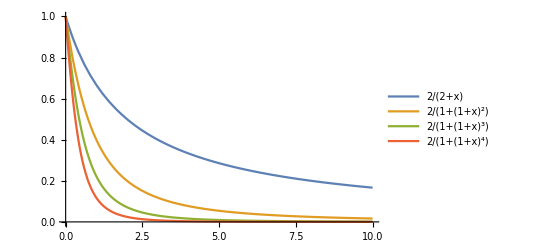

```mathematica
Plot[funcsShiftA,{x,0,10},PlotRange->{{0,10},{0,1}},PlotLegends->"Expressions"]
```

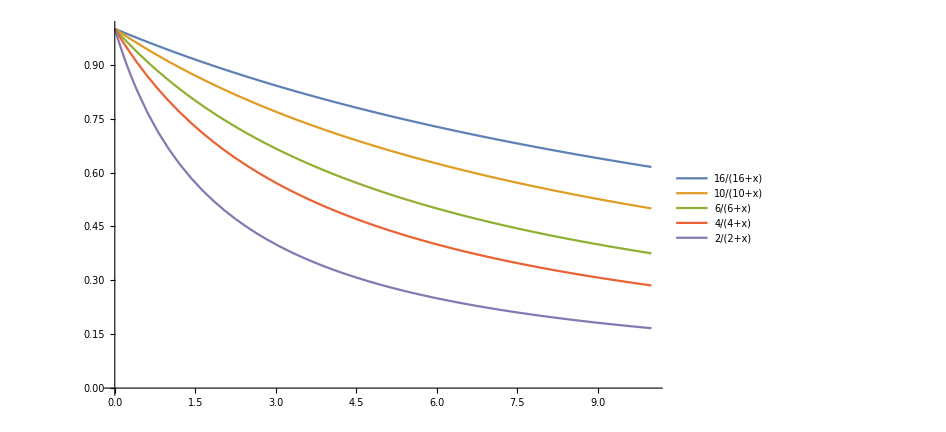

```mathematica
Plot[funcsShiftB1,{x,0,10},PlotRange->{{0,10},{0,1}},PlotLegends->"Expressions",ImageSize->700]
```

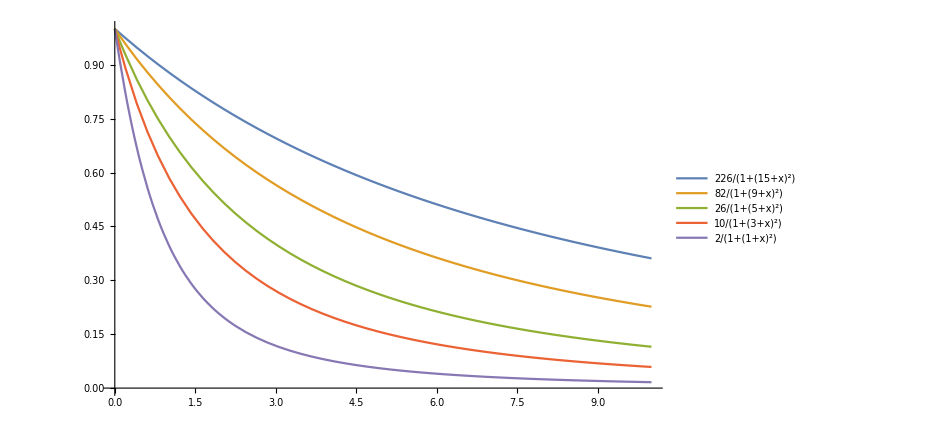

```mathematica
Plot[funcsShiftB2,{x,0,10},PlotRange->{{0,10},{0,1}},PlotLegends->"Expressions",ImageSize->700]
```

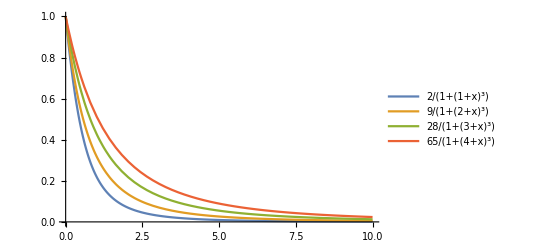

```mathematica
Plot[funcsShiftB3,{x,0,10},PlotRange->{{0,10},{0,1}},PlotLegends->"Expressions"]
```

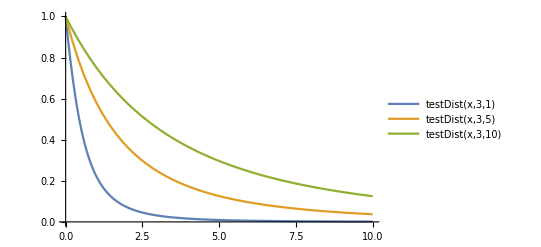

```mathematica
Plot[{testDist[x,3,1],testDist[x,3,5],testDist[x,3,10]},{x,0,10},PlotRange->{{0,10},{0,1}},PlotLegends->"Expressions"]
```

```mathematica
result=Solve[testDist[x,a,b]==c,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-b+(-(-1-b^a+c)/c)^(1/a)}}

```mathematica
result/.{b->2,c->57/100,a->4}//N
```

{{x→0.317078}}

## Plot ‘em all (in terms of RB)

```mathematica
RBPlotRange={{1,10},{0,1}};
```

```mathematica
RBPlotRangeMid={{1,100},{0,1}};
```

```mathematica
RBPlotRangeExt={{1,1000},{0,1}};
```

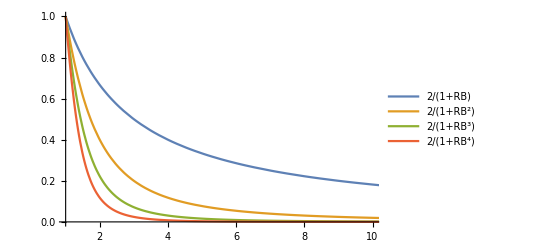

```mathematica
Plot[funcsShiftARB,{RB,1,100},PlotRange->RBPlotRange,PlotLegends->"Expressions"]
```

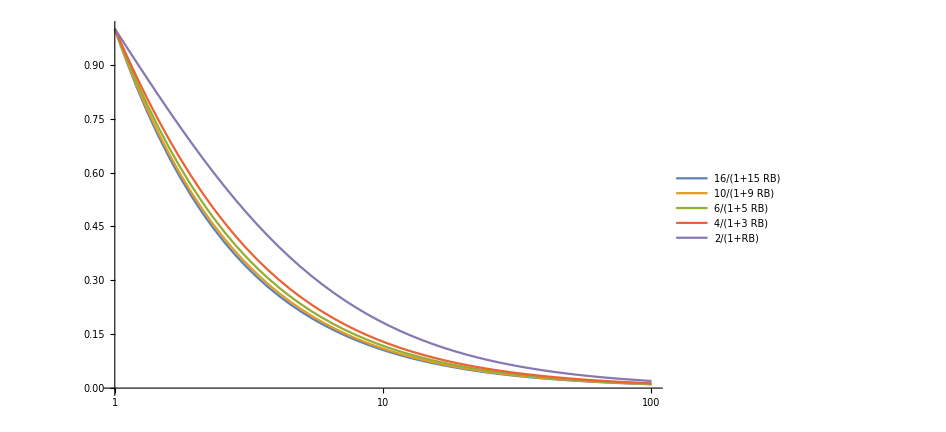

```mathematica
LogLinearPlot[funcsShiftB1RB,{RB,1,100},PlotRange->RBPlotRangeMid,PlotLegends->"Expressions",ImageSize->700]
```

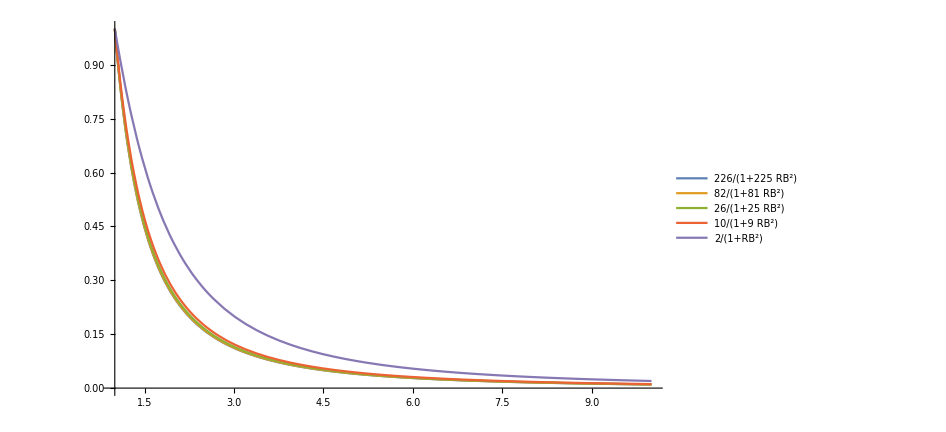

```mathematica
Plot[funcsShiftB2RB,{RB,1,10},PlotRange->RBPlotRange,PlotLegends->"Expressions",ImageSize->700]
```

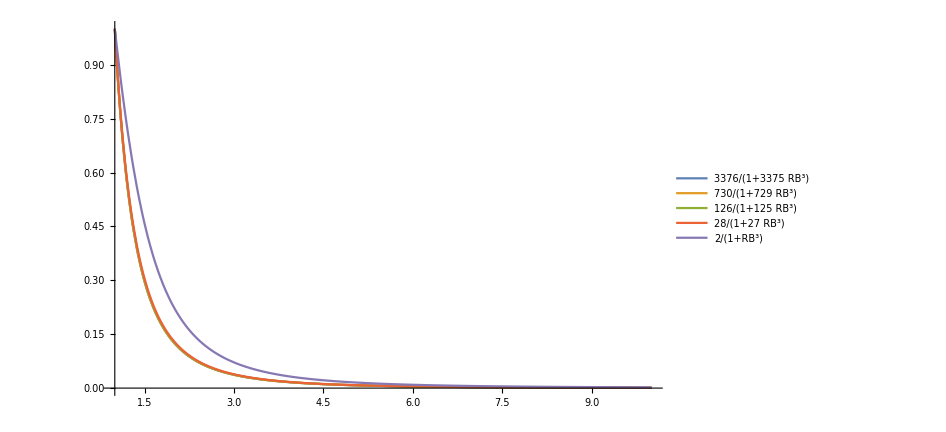

```mathematica
Plot[funcsShiftB3RB,{RB,1,10},PlotRange->RBPlotRange,PlotLegends->"Expressions",ImageSize->700]
```

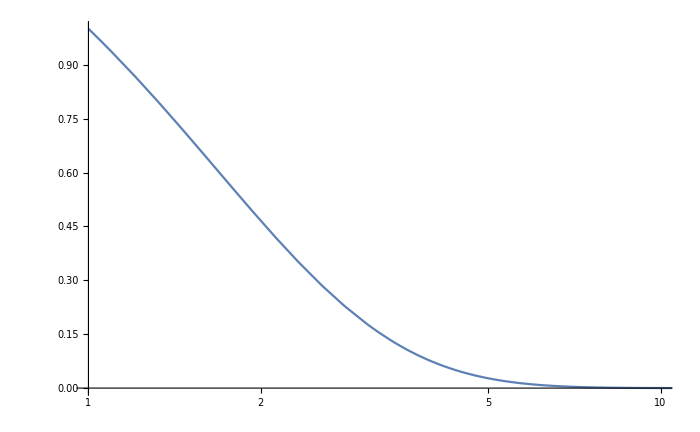

```mathematica
LogLinearPlot[testDistRBExp[RB,1,2],{RB,1,100},PlotRange->RBPlotRange,PlotLegends->"Expressions",ImageSize->700]
```

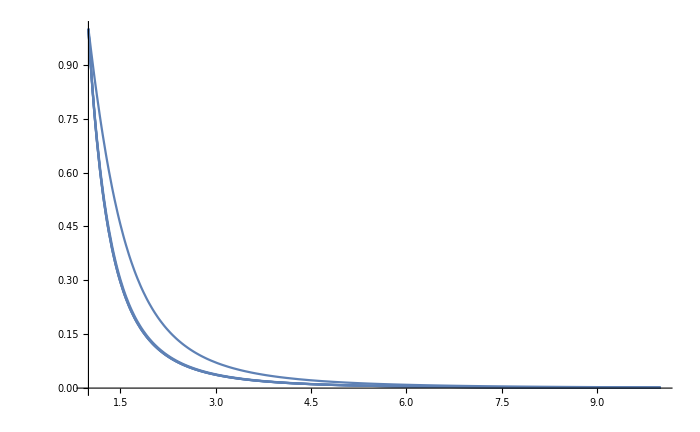

```mathematica
Plot[funcsShiftBARB[3],{RB,1,10},PlotRange->RBPlotRange,PlotLegends->"Expressions",ImageSize->700]
```

```mathematica
resultRB=Solve[testDistRB[RB,a,b]==c,RB]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{RB→(-(b^-a (-1-b^a+c))/c)^(1/a)}}

```mathematica
potAbove=941;potTot=2000;
```

```mathematica
(potTot-potAbove)/potTot//N
```

0.5295

```mathematica
resultRB/.{b->0.5,c->(potTot-potAbove)/potTot,a->0.5}//N
```

{{RB→9.89233}}

```mathematica
4*19.28
```

77.12

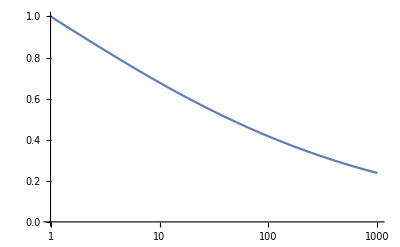

```mathematica
LogLinearPlot[testDistRB[RB,0.29,1],{RB,1,1000},PlotRange->RBPlotRangeExt]
```

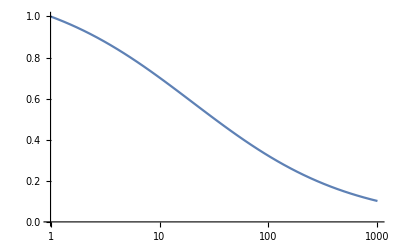

```mathematica
LogLinearPlot[testDistRB[RB,0.6,0.05],{RB,1,1000},PlotRange->RBPlotRangeExt]
```

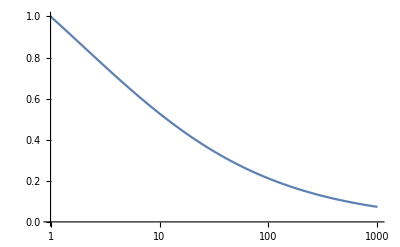

```mathematica
LogLinearPlot[testDistRB[RB,0.5,0.5],{RB,1,1000},PlotRange->RBPlotRangeExt]
```

## None of these seem to be working ... Try exponential, you suppose?

```mathematica
Exp/@-{0.1,0.2,0.3,0.4,0.5,0.55,0.56,0.567143}//N
```

{0.904837,0.818731,0.740818,0.67032,0.606531,0.57695,0.571209,0.567143}

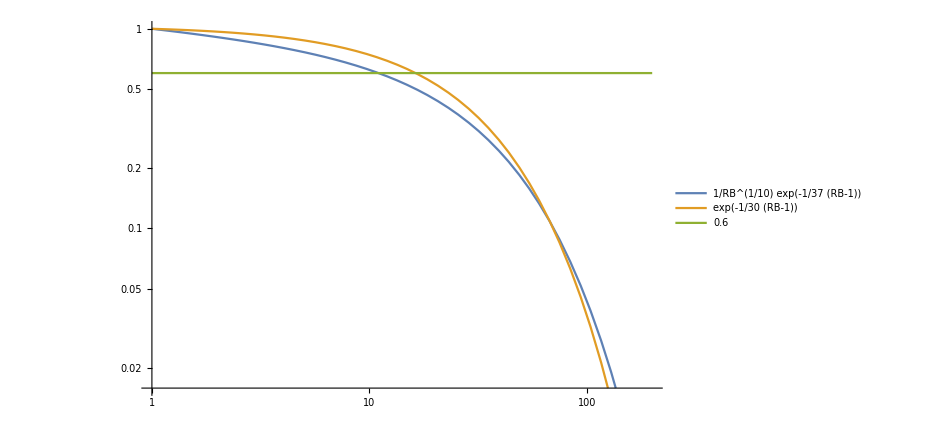

```mathematica
LogLogPlot[{RB^(-1/10) Exp[-1/37(RB-1)], Exp[-1/30(RB-1)],0.6},{RB,1,200},ImageSize->700,PlotLegends->"Expressions"]
```

Man, it barely does the job

```mathematica
Exp[-19/30]//N
```

0.530819

## So now define distribution funcs

## Distribution functions at source

#### Step function definition

```mathematica
sourcePieceFunc[vpar_,vperp_,vbth_,RB_]:=Piecewise[{{1,Im[Sqrt[vperp^2(1-RB)+vpar^2+vbth^2(1-Exp[-1/30(RB-1)])]]==0&&vpar>0},{0,vpar≤ 0},{0,vperp^2(1-RB)+vpar^2+vbth^2≤ 0}}]
```

#### Kappa and Maxwellian functions at source assumes Π(R_B= 1) = 0

```mathematica
sourceFuncMaxwellian[vpar0_,vperp0_,vbth0_,RB_]:=1/π^(3/2)Exp[-(vpar0^2+vperp0^2)]sourcePieceFunc[vpar0,vperp0,vbth0,RB]
```

```mathematica
sourceFuncKappa[vpar0_,vperp0_,vbth0_,RB_,kappa_]:=1/(π^(3/2)(1-3/(2 kappa))^(3/2))Gamma[kappa+1]/(kappa^(3/2)Gamma[kappa-1/2])(1+(vpar0^2+vperp0^2)/(kappa-3/2))^(-(kappa+1))sourcePieceFunc[vpar0,vperp0,vbth0,RB]
```

```mathematica
midFuncMaxwellian[vpar_,vperp_,vbth0_,RB_]:=1/π^(3/2)Exp[-(vpar^2+vperp^2+vbth0^2(Exp[-1/30(RB-1)]-1))]UnitStep[vpar](*sourcePieceFunc[vpar0,vperp0,vbth0,RB]*)
```

```mathematica
midFuncKappa[vpar_,vperp_,vbth0_,RB_,kappa_]:=1/(π^(3/2)(1-3/(2 kappa))^(3/2))Gamma[kappa+1]/(kappa^(3/2)Gamma[kappa-1/2])(1+(vpar^2+vperp^2+vbth0^2(Exp[-1/30(RB-1)]-1))/(kappa-3/2))^(-(kappa+1))UnitStep[vpar](*sourcePieceFunc[vpar0,vperp0,vbth0,RB]*)
```

#### Put all the accel toward vPar

```mathematica
midFuncKappa[vpar_,vperp_,vbth0_,RB_,kappa_]:=1/(π^(3/2)(1-3/(2 kappa))^(3/2))Gamma[kappa+1]/(kappa^(3/2)Gamma[kappa-1/2])(1+((vpar-vbth0 Sqrt[1-Exp[-1/30(RB-1)]])^2+vperp^2 RB)/(kappa-3/2))^(-(kappa+1))UnitStep[vpar](*sourcePieceFunc[vpar0,vperp0,vbth0,RB]*)
```

Whole new thang

```mathematica
midFuncMaxwellian[vpar_,vperp_,vbth0_,RB_]:=1/π^(3/2)Exp[-((vpar-vbth0(1-Exp[-1/30(RB-1)])^(1/2))^2+vperp^2 RB)](*sourcePieceFunc[vpar0,vperp0,vbth0,RB]*)
```

… And a whole new thang

```mathematica
midFuncMaxwellian[vpar_,vperp_,vbth0_,alpha_]:=1/π^(3/2)Exp[-(vperp^2+vpar^2+vbth0^2(1-Exp[-1/30(1/alpha-1)])-2 vbth0(1-Exp[-1/30(1/alpha-1)])^(1/2)(vpar^2+(1-alpha)vperp^2)^(1/2))]UnitStep[vpar](*sourcePieceFunc[vpar0,vperp0,vbth0,RB]*)
```

… Der neueste!

```mathematica
midFuncMaxwellian2[vpar_,vperp_,vbth0_,alpha_]:=1/π^(3/2)Exp[-(vperp^2+vpar^2-2 vbth0(1-Exp[-1/30(1/alpha-1)])^(1/2)(vpar^2+(1-alpha)vperp^2-vbth0^2(1-Exp[-1/30(1/alpha-1)]))^(1/2))]UnitStep[vpar](*sourcePieceFunc[vpar0,vperp0,vbth0,RB]*)
```

```mathematica
vbthK[dPhi_,Tm_,kappa_]:=√(dPhi/(Tm(1-3/(2 kappa))));
vbth[dPhi_,Tm_]:=√(dPhi/Tm);
```

```mathematica
midFuncMaxwellCyl[rho_,phi_,vbth_,alpha_]:=2/(√π)Exp[-(rho^2-2 vbth(1-Exp[-1/30(1/alpha-1)])^(1/2)(rho^2(1-alpha (Sin[phi])^2)-vbth^2(1-Exp[-1/30(1/alpha-1)]))^(1/2))];
midFuncMaxwellCylUnitStep[rho_,phi_,vbth_,alpha_]:=2/(√π)Exp[-(rho^2-2 vbth(1-Exp[-1/30(1/alpha-1)])^(1/2)(rho^2(1-alpha (Sin[phi])^2)-vbth^2(1-Exp[-1/30(1/alpha-1)]))^(1/2))]UnitStep[rho^2(1-alpha(Sin[phi])^2)-vbth^2(1-Exp[-1/30(1/alpha-1)])];
```

```mathematica
midFuncKappaCyl[rho_,phi_,vbth_,alpha_,kappa_]:=2/(√π(1-3/(2kappa))^(3/2))Gamma[kappa+1]/(kappa^(3/2)Gamma[kappa-1/2])(1+(rho^2-2 vbth(1-Exp[-1/30(1/alpha-1)])^(1/2)(rho^2(1-alpha (Sin[phi])^2)-vbth^2(1-Exp[-1/30(1/alpha-1)]))^(1/2))/(kappa-3/2))^(-(kappa+1))
```

```mathematica
midFuncKappaCylUnitStep[rho_,phi_,vbth_,alpha_,kappa_]:=2/(√π(1-3/(2kappa))^(3/2))Gamma[kappa+1]/(kappa^(3/2)Gamma[kappa-1/2])(1+(rho^2-2 vbth(1-Exp[-1/30(1/alpha-1)])^(1/2)(rho^2(1-alpha (Sin[phi])^2)-vbth^2(1-Exp[-1/30(1/alpha-1)]))^(1/2))/(kappa-3/2))^(-(kappa+1))UnitStep[rho^2(1-alpha(Sin[phi])^2)-vbth^2(1-Exp[-1/30(1/alpha-1)])];
```

## Distribution Function Plots (looks nice, the mapping is reaaal nice)

```mathematica
vbthTot=√(2200/110)//N
```

4.47214

### Function at source, with lines showing which particles make it to the bottom (I think)

```mathematica
Manipulate[Plot3D[sourceFuncKappa[vpar,vperp,vbth,RB,kappa],{vpar,0,3},{vperp,-1.5,1.5},PlotRange->Full,ImageSize->700],{RB,{1,3/2,2,5/2,3,10,30,50,70,100,200,300,500,700,1000}},{vbth,0,5},{{kappa,2},3/2,10}]
```

### Function along field line

```mathematica
Manipulate[Plot3D[midFuncMaxwellian2[vpar,vperp,vbth,alpha],{vpar,0,10},{vperp,-6,6},PlotRange->Full,ImageSize->700,PlotPoints->50],{alpha,1/{1,3/2,2,5/2,3,10,30,50,70,100,200,300,500,700,1000}},{{vbth,vbthTot},0,5}]
```

### Parametric kappa plot

```mathematica
dPhi=2200;Tm=110;kaps=18/10;
```

```mathematica
Manipulate[ParametricPlot3D[{rho Cos[phi],rho Sin[phi],midFuncKappaCyl[rho,phi,vbth[dPhi,Tm],alpha,kaps]},{rho,0,10},{phi,-π/2,π/2},PlotRange->All,PlotPoints->50,ImageSize->800],{{alpha,125/10000},0,1}]
```

```mathematica
ParametricPlot3D[{rho Cos[phi],rho Sin[phi],midFuncMaxwellCyl[rho,phi,vbth[dPhi,Tm],0.05]},{rho,0,6},{phi,-π/2,π/2},PlotRange->All,PlotPoints->20,ImageSize->800]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{rho Cos[phi],rho Sin[phi],midFuncMaxwellCyl[rho,phi,vbth[dPhi,Tm],0.0125]},{rho,0,8},{phi,-π/2,π/2},PlotRange->All,PlotPoints->20,ImageSize->800]
```

-Graphics3D-

## Now, NIntegrate ‘em!

#### Params for plot

```mathematica
dPhi=2200;Tm=110;kaps=18/10;
```

#### Some plot options

```mathematica
colors={Black,Gray,Orange,Red,Brown,Green,Purple};
kappas = {1.55,1.6,1.8,2,2.45,4};
```

```mathematica
placeList={Above,Above,Above,Above,Above,Above,Above};
nDigs={3,2,2,2,3,1,2,2};
kapStrVals=Table[NumberForm[kappas[[k]],nDigs[[k]]],{k,1,6}];
kappaLabels=Table[StringForm["κ = `1`",kapStrVals[[k]]],{k,1,6}];
nDigitsdPhi=3;nDigitsTm=3;
RBMin=1;RBMax=10000;
```

```mathematica
showers={1,2,3,4,5,6};
(*showers={1};*)
```

```mathematica
(*Show[Table[LogLogPlot[NIntegrate[rho^2 Sin[phi]  normFacAlt[vbth[dPhi,Tm],kappas[[k]]]funcAlt[rho,phi,vbth[dPhi,Tm],kappas[[k]],1/RB],{rho,0,∞},{phi,0,π/2}],{RB,RBMin,RBMax},PlotRange->{{RBMin,RBMax},{1,1000}},PlotStyle->colors[[k]],Frame->True,PlotLabels ->Placed[kappaLabels[[k]] ,placeList[[k]]],LabelStyle->(FontSize->19),FrameLabel->{{StringForm["n/n_0= R_κ(ΔΦ, T, κ, R_B)"],""},{StringForm["Mirror Ratio R_B"],StringForm["ΔΦ = `1`; T_m= `2` eV; ϕ̄= `3`",NumberForm[dPhi,nDigitsdPhi],NumberForm[Tm,nDigitsTm],NumberForm[N[dPhi/Tm],{3,1}]]}},ImageSize->900],{k,showers}],LogLogPlot[NIntegrate[rho^2 Sin[phi] midFuncMaxwellCyl[rho,phi,vbth[dPhi,Tm],1/RB],{vpar,0,∞},{vperp,0,∞}],{RB,RBMin,RBMax},PlotRange->{{RBMin,RBMax},{1,1000}},PlotStyle->Black,Frame->True,FrameStyle->Black,PlotLabels ->Placed[StringForm["Barbosa [1977]"] ,Above],LabelStyle->(FontSize->19),FrameLabel->{{StringForm["n/n_0= R_κ(ΔΦ, T, κ, R_B)"],""},{StringForm["Mirror Ratio R_B"],StringForm["ΔΦ = `1`; T_m= `2` eV; ϕ̄= `3`",NumberForm[dPhi,nDigitsdPhi],NumberForm[Tm,nDigitsTm],NumberForm[N[dPhi/Tm],{3,1}]]}},ImageSize->900]]*)
```

```mathematica
Plot[NIntegrate[rho^2 Sin[phi] midFuncMaxwellCylUnitStep[rho,phi,vbth[dPhi,Tm],1/RB],{rho,0,6},{phi,0,π/2}],{RB,1,10},PlotRange->{{RBMin,RBMax},Automatic},PlotStyle->Black,Frame->True,FrameStyle->Black,PlotLabels ->Placed[StringForm["Spence [1977]"] ,Above],LabelStyle->(FontSize->19),FrameLabel->{{StringForm["n/n_0= R_κ(ΔΦ, T, κ, R_B)"],""},{StringForm["Mirror Ratio R_B"],StringForm["ΔΦ = `1`; T_m= `2` eV; ϕ̄= `3`",NumberForm[dPhi,nDigitsdPhi],NumberForm[Tm,nDigitsTm],NumberForm[N[dPhi/Tm],{3,1}]]}},ImageSize->900]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.504246 and 7.80194×10^-7 for the integral and error estimates.

$Aborted

```mathematica
vbth[dPhi,Tm]//N
```

4.47214

## Tons of NIntegration

### Tons of baby lil’ Maxwellian NIntegrates

```mathematica
NIntegrate[rho^2 Sin[phi] midFuncMaxwellCylUnitStep[rho,phi,vbth[dPhi,Tm],1/2],{rho,0,6},{phi,0,π/2}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in rho near {rho,phi} = {1.14512,1.5617276690338959023451881336086444207467138767242431640625}. NIntegrate obtained 1.39774 and 0.0000187616 for the integral and error estimates.

1.39774

```mathematica
NIntegrate[rho^2 Sin[phi] midFuncMaxwellCylUnitStep[rho,phi,vbth[dPhi,Tm],1],{rho,0,6},{phi,0,π/2}]
```

0.5

```mathematica
NIntegrate[rho^2 Sin[phi] midFuncMaxwellCylUnitStep[rho,phi,vbth[dPhi,Tm],1/3],{rho,0,6},{phi,0,π/2}]
```

2.13056

```mathematica
NIntegrate[rho^2 Sin[phi] midFuncMaxwellCylUnitStep[rho,phi,vbth[dPhi,Tm],1/4],{rho,0,6},{phi,0,π/2}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in rho near {rho,phi} = {1.59208,1.510961155740288629212297877302262349985539913177490234375}. NIntegrate obtained 3.03344 and 5.50678×10^-6 for the integral and error estimates.

3.03344

```mathematica
NIntegrate[rho^2 Sin[phi] midFuncMaxwellCylUnitStep[rho,phi,vbth[dPhi,Tm],1/5],{rho,0,6},{phi,0,π/2}]
```

3.79897

```mathematica
NIntegrate[rho^2 Sin[phi] midFuncMaxwellCylUnitStep[rho,phi,vbth[dPhi,Tm],1/7],{rho,0,6},{phi,0,π/2}]
```

5.42184

```mathematica
NIntegrate[rho^2 Sin[phi] midFuncMaxwellCylUnitStep[rho,phi,vbth[dPhi,Tm],1/8],{rho,0,6},{phi,0,π/2}]
```

6.21512

```mathematica
NIntegrate[rho^2 Sin[phi] midFuncMaxwellCylUnitStep[rho,phi,vbth[dPhi,Tm],1/10],{rho,0,6},{phi,0,π/2}]
```

7.76774

```mathematica
NIntegrate[rho^2 Sin[phi] midFuncMaxwellCylUnitStep[rho,phi,vbth[dPhi,Tm],1/15],{rho,0,6},{phi,0,π/2}]
```

11.4621

```mathematica
NIntegrate[rho^2 Sin[phi] midFuncMaxwellCylUnitStep[rho,phi,vbth[dPhi,Tm],1/18],{rho,0,6},{phi,0,π/2}]
```

13.5422

```mathematica
NIntegrate[rho^2 Sin[phi] midFuncMaxwellCylUnitStep[rho,phi,vbth[dPhi,Tm],1/20],{rho,0,6},{phi,0,π/2}]
```

14.8581

```mathematica
(NIntegrate[rho^2 Sin[phi] midFuncMaxwellCylUnitStep[rho,phi,vbth[dPhi,Tm],#],{rho,0,12},{phi,0,π/2}])&/@{1/20,1/25,1/30,1/40,1/50,1/60,1/70,1/80}
```

{14.9091,18.1004,21.0427,26.2137,30.5141,34.0598,36.9702,39.357}

```mathematica
(NIntegrate[rho^2 Sin[phi] midFuncMaxwellCylUnitStep[rho,phi,vbth[dPhi,Tm],#],{rho,0,12},{phi,0,π/2}])&/@{1/100,1/200,1/300,1/500,1/700,1/1000,1/2000}
```

{42.9361,50.2171,52.5386,54.4421,55.2817,55.9215,56.6788}

```mathematica
alphaList={1,1/2,1/3,1/4,1/5,1/7,1/8,1/10,1/15,1/18,1/20,1/25,1/30,1/40,1/50,1/60,1/70,1/80,1/100,1/200,1/300,1/500,1/700,1/1000,1/2000};
```

```mathematica
RBList=1/alphaList
```

{1,2,3,4,5,7,8,10,15,18,20,25,30,40,50,60,70,80,100,200,300,500,700,1000,2000}

### Tons of baby lil’ kappa NIntegrates

```mathematica
alphaListP1={1,1/2,1/3,1/4,1/5,1/7,1/8,1/10};
```

```mathematica
alphaListP2={1/15,1/18,1/20,1/25,1/30,1/40,1/50,1/60,1/70,1/80};
```

```mathematica
alphaListP3={1/100,1/200,1/300,1/500,1/700,1/1000,1/2000};
```

```mathematica
kappaEq2P1=(NIntegrate[rho^2 Sin[phi] midFuncKappaCylUnitStep[rho,phi,vbth[dPhi,Tm],#,2],{rho,0,10},{phi,0,π/2}])&/@alphaListP1
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in rho near {rho,phi} = {1.14261,1.50304582074961136373136838528807857073843479156494140625}. NIntegrate obtained 1.42784 and 9.25049×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in rho near {rho,phi} = {1.59297,1.55641289484209189609986712099498618044890463352203369140625}. NIntegrate obtained 3.03494 and 6.23907×10^-6 for the integral and error estimates.

{0.499703,1.42784,2.13167,3.03494,3.80669,5.40743,6.20069,7.78006,11.6971,14.0254,15.5674,19.3819,23.1308,30.3963,37.304,43.8139,49.9053,55.5746,65.6941,98.4491,115.687,133.486,142.587,150.124,159.802}

```mathematica
kappaEq2P2=(NIntegrate[rho^2 Sin[phi] midFuncKappaCylUnitStep[rho,phi,vbth[dPhi,Tm],#,2],{rho,0,10},{phi,0,π/2}])&/@alphaListP2
```

{11.6971,14.0254,15.5674,19.3819,23.1308,30.3963,37.304,43.8139,49.9053,55.5746}

```mathematica
kappaEq2P3=(NIntegrate[rho^2 Sin[phi] midFuncKappaCylUnitStep[rho,phi,vbth[dPhi,Tm],#,2],{rho,0,10},{phi,0,π/2}])&/@alphaListP3
```

```mathematica
kappaEq2List={0.499702579763253,1.4278380591282467,2.1316719757826057,3.0349427589993625,3.8066939137945615,5.407433104956269,6.200687553405672,7.780063344560573,11.697082545162969,14.025405867279854,15.567387157013885,19.381897617472788,23.130794142072205,30.39633402870971,37.30399425218055,43.81388515533611,49.90532694530409,55.57463441597329,65.69407845322915,98.44909501507566,115.68701806444984,133.4856400889652,142.58675522687966,150.12356897776178,159.8018985038659}
```

{0.499703,1.42784,2.13167,3.03494,3.80669,5.40743,6.20069,7.78006,11.6971,14.0254,15.5674,19.3819,23.1308,30.3963,37.304,43.8139,49.9053,55.5746,65.6941,98.4491,115.687,133.486,142.587,150.124,159.802}

```mathematica
NIntegrate[rho^2 Sin[phi] midFuncKappaCylUnitStep[rho,phi,vbth[dPhi,Tm],1,2],{rho,0,10},{phi,0,π/2}]
```

### Yeah whatever, now make some plots

```mathematica
MaxwellIntegList={0.5000000100192846,1.397739993166385,2.130559401096317,3.0334356841054544,3.798967164778606,5.421841250634384,6.215121441482832,7.767744275502014,11.462051789098805,13.542151706922304,14.909129379477323,18.100350217242553,21.04271888629097,26.213687037782066,30.51410075572467,34.05977754960439,36.970228106817004,39.356976965121866,42.936091154826826,50.21709817052893,52.53864161632981,54.44213649245443,55.281743335387006,55.92145112391653,56.678796233161364}
```

{0.5,1.39774,2.13056,3.03344,3.79897,5.42184,6.21512,7.76774,11.4621,13.5422,14.9091,18.1004,21.0427,26.2137,30.5141,34.0598,36.9702,39.357,42.9361,50.2171,52.5386,54.4421,55.2817,55.9215,56.6788}

```mathematica
RBList[[11]]
```

20

```mathematica
MaxwellIntegList[[11]]
```

14.9091

```mathematica
partList=Partition[Riffle[RBList,MaxwellIntegList],2]
```

```mathematica
kappaEq2PlotList=Partition[Riffle[RBList,kappaEq2List],2]
```

{{1,0.499703},{2,1.42784},{3,2.13167},{4,3.03494},{5,3.80669},{7,5.40743},{8,6.20069},{10,7.78006},{15,11.6971},{18,14.0254},{20,15.5674},{25,19.3819},{30,23.1308},{40,30.3963},{50,37.304},{60,43.8139},{70,49.9053},{80,55.5746},{100,65.6941},{200,98.4491},{300,115.687},{500,133.486},{700,142.587},{1000,150.124},{2000,159.802}}

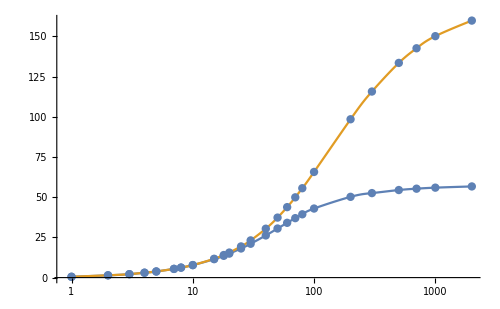

```mathematica
ListLogLinearPlot[{partList,kappaEq2PlotList},Joined->True,InterpolationOrder->3,Mesh->Full,ImageSize->500]
```